```mathematica
Clear[n, g]
```

```mathematica
M = {{Δ/2,g Sqrt[n+1] },{g Sqrt[n+1] ,-Δ/2}}
```

{{Δ/2,g √(1+n)},{g √(1+n),-Δ/2}}

```mathematica
{{Δ/2,a g},{b g,-Δ/2}}
```

{{Δ/2,a g},{b g,-Δ/2}}

```mathematica
MatrixForm[M]
```

(Δ/2 | g √(1+n)
g √(1+n) | -Δ/2)

```mathematica
MatrixExp[-I t M]
```

{{-(ⅇ^(-1/2 ⅈ t √(4 g^2+4 g^2 n+Δ^2)) (-Δ-√(4 g^2+4 g^2 n+Δ^2)))/(2 √(4 g^2+4 g^2 n+Δ^2))+(ⅇ^(1/2 ⅈ t √(4 g^2+4 g^2 n+Δ^2)) (-Δ+√(4 g^2+4 g^2 n+Δ^2)))/(2 √(4 g^2+4 g^2 n+Δ^2)),(ⅇ^(-1/2 ⅈ t √(4 g^2+4 g^2 n+Δ^2)) g √(1+n))/(√(4 g^2+4 g^2 n+Δ^2))-(ⅇ^(1/2 ⅈ t √(4 g^2+4 g^2 n+Δ^2)) g √(1+n))/(√(4 g^2+4 g^2 n+Δ^2))},{(ⅇ^(-1/2 ⅈ t √(4 g^2+4 g^2 n+Δ^2)) g √(1+n))/(√(4 g^2+4 g^2 n+Δ^2))-(ⅇ^(1/2 ⅈ t √(4 g^2+4 g^2 n+Δ^2)) g √(1+n))/(√(4 g^2+4 g^2 n+Δ^2)),-(ⅇ^(-1/2 ⅈ t √(4 g^2+4 g^2 n+Δ^2)) (Δ-√(4 g^2+4 g^2 n+Δ^2)))/(2 √(4 g^2+4 g^2 n+Δ^2))+(ⅇ^(1/2 ⅈ t √(4 g^2+4 g^2 n+Δ^2)) (Δ+√(4 g^2+4 g^2 n+Δ^2)))/(2 √(4 g^2+4 g^2 n+Δ^2))}}

```mathematica
U = FullSimplify[%];
MatrixForm[U]
```

(Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]-(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)) | -(2 ⅈ g √(1+n) Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2))
-(2 ⅈ g √(1+n) Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)) | Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]+(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)))

```mathematica
SubMinus[U]= {{Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]+(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)),(2 ⅈ g √(1+n) Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2))},{(2 ⅈ g √(1+n) Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)),Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]-(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2))}};
MatrixForm[SubMinus[U]]
```

(Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]+(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)) | (2 ⅈ g √(1+n) Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2))
(2 ⅈ g √(1+n) Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)) | Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]-(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)))

```mathematica
sigmaMas = {{0,1},{0,0}};
MatrixForm[sigmaMas]
```

(0 | 1
0 | 0)

```mathematica
sigmaMenos = {{0,0},{1,0}};
MatrixForm[sigmaMenos]
```

(0 | 0
1 | 0)

```mathematica
sigmaMas = FullSimplify[SubMinus[U].sigmaMas.U];
MatrixForm[sigmaMas]
```

((g √(1+n) (Δ-Δ Cos[t √(4 g^2 (1+n)+Δ^2)]-ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]))/(4 g^2 (1+n)+Δ^2) | (Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]+(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)))^2
-(2 g^2 (1+n) (-1+Cos[t √(4 g^2 (1+n)+Δ^2)]))/(4 g^2 (1+n)+Δ^2) | (g √(1+n) (-Δ+Δ Cos[t √(4 g^2 (1+n)+Δ^2)]+ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]))/(4 g^2 (1+n)+Δ^2))

```mathematica
sigmaMenos = FullSimplify[SubMinus[U].sigmaMenos.U];
MatrixForm[sigmaMenos]
```

((g √(1+n) (Δ-Δ Cos[t √(4 g^2 (1+n)+Δ^2)]+ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]))/(4 g^2 (1+n)+Δ^2) | -(2 g^2 (1+n) (-1+Cos[t √(4 g^2 (1+n)+Δ^2)]))/(4 g^2 (1+n)+Δ^2)
(Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]-(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)))^2 | (g √(1+n) (-Δ+Δ Cos[t √(4 g^2 (1+n)+Δ^2)]-ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]))/(4 g^2 (1+n)+Δ^2))

```mathematica
G = sigmaMas.sigmaMenos
```

{{(Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]-(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)))^2 (Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]+(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)))^2+(g^2 (1+n) (Δ-Δ Cos[t √(4 g^2 (1+n)+Δ^2)]-ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]) (Δ-Δ Cos[t √(4 g^2 (1+n)+Δ^2)]+ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]))/((4 g^2 (1+n)+Δ^2)^2),-(2 g^3 (1+n)^(3/2) (-1+Cos[t √(4 g^2 (1+n)+Δ^2)]) (Δ-Δ Cos[t √(4 g^2 (1+n)+Δ^2)]-ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]))/((4 g^2 (1+n)+Δ^2)^2)+(g √(1+n) (Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]+(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)))^2 (-Δ+Δ Cos[t √(4 g^2 (1+n)+Δ^2)]-ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]))/(4 g^2 (1+n)+Δ^2)},{-(2 g^3 (1+n)^(3/2) (-1+Cos[t √(4 g^2 (1+n)+Δ^2)]) (Δ-Δ Cos[t √(4 g^2 (1+n)+Δ^2)]+ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]))/((4 g^2 (1+n)+Δ^2)^2)+(g √(1+n) (Cos[1/2 t √(4 g^2 (1+n)+Δ^2)]-(ⅈ Δ Sin[1/2 t √(4 g^2 (1+n)+Δ^2)])/(√(4 g^2 (1+n)+Δ^2)))^2 (-Δ+Δ Cos[t √(4 g^2 (1+n)+Δ^2)]+ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]))/(4 g^2 (1+n)+Δ^2),(4 g^4 (1+n)^2 (-1+Cos[t √(4 g^2 (1+n)+Δ^2)])^2)/((4 g^2 (1+n)+Δ^2)^2)+(g^2 (1+n) (-Δ+Δ Cos[t √(4 g^2 (1+n)+Δ^2)]-ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]) (-Δ+Δ Cos[t √(4 g^2 (1+n)+Δ^2)]+ⅈ √(4 g^2 (1+n)+Δ^2) Sin[t √(4 g^2 (1+n)+Δ^2)]))/((4 g^2 (1+n)+Δ^2)^2)}}

Estado inicial |g,n+1 ⟩, donde |n+1 ⟩ es un estado coherente

```mathematica
omegaN[n_,Ω_]:=Sqrt[(Δ/2)^2+ Ω^2 (n+1)]
```

```mathematica
I1[Ω_,n_,Γ_,ω_,t_]:= ((Ω Sqrt[n+1])^4/((omegaN[n+1,Ω]^2)(omegaN[n,Ω]^2)))Abs[(ⅇ^(-ⅈ t ω) (-ⅇ^(t Γ) (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2) √(Δ^2+4 (1+n) Ω^2) Cos[1/2 t √(Δ^2+4 (1+n) Ω^2)] Sin[1/2 t √(Δ^2+4 n Ω^2)]+ⅇ^(t Γ) √(Δ^2+4 n Ω^2) Cos[1/2 t √(Δ^2+4 n Ω^2)] ((Γ-ⅈ ω) √(Δ^2+4 (1+n) Ω^2) Cos[1/2 t √(Δ^2+4 (1+n) Ω^2)]+(-Γ^2+2 ⅈ Γ ω+ω^2+Ω^2) Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)])+(Γ-ⅈ ω) (-ⅇ^(ⅈ t ω) √(Δ^2+4 n Ω^2) √(Δ^2+4 (1+n) Ω^2)+ⅇ^(t Γ) (2 Γ^2+Δ^2-4 ⅈ Γ ω-2 ω^2+2 Ω^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)])))/(2 (Γ^4-4 ⅈ Γ^3 ω-Δ^2 ω^2+ω^4-2 ω^2 Ω^2-4 n ω^2 Ω^2+Ω^4+Γ^2 (Δ^2-6 ω^2+2 (1+2 n) Ω^2)-2 ⅈ Γ ω (Δ^2-2 ω^2+2 (1+2 n) Ω^2)))]^2
```

```mathematica
I2[Ω_,n_,Γ_,ω_,t_]:= ((Ω Sqrt[n+1])^2/(omegaN[n+1,Ω]^2))Abs[(ⅇ^(-ⅈ t ω) (ⅇ^(ⅈ t ω) Γ^2 √(Δ^2+4 (1+n) Ω^2)-2 ⅈ ⅇ^(ⅈ t ω) Γ ω √(Δ^2+4 (1+n) Ω^2)-ⅇ^(ⅈ t ω) ω^2 √(Δ^2+4 (1+n) Ω^2)+ⅇ^(ⅈ t ω) Ω^2 √(Δ^2+4 (1+n) Ω^2)-ⅇ^(t Γ) (Γ-ⅈ ω) √(Δ^2+4 n Ω^2) √(Δ^2+4 (1+n) Ω^2) Cos[1/2 t √(Δ^2+4 (1+n) Ω^2)] Sin[1/2 t √(Δ^2+4 n Ω^2)]+ⅇ^(t Γ) Γ^2 √(Δ^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)]-2 ⅈ ⅇ^(t Γ) Γ ω √(Δ^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)]-ⅇ^(t Γ) ω^2 √(Δ^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)]-ⅇ^(t Γ) Ω^2 √(Δ^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)]-ⅇ^(t Γ) Cos[1/2 t √(Δ^2+4 n Ω^2)] ((Γ^2-2 ⅈ Γ ω-ω^2+Ω^2) √(Δ^2+4 (1+n) Ω^2) Cos[1/2 t √(Δ^2+4 (1+n) Ω^2)]-(Γ-ⅈ ω) (2 Γ^2+Δ^2-4 ⅈ Γ ω-2 ω^2+2 Ω^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)])))/(2 (Γ^4-4 ⅈ Γ^3 ω-Δ^2 ω^2+ω^4-2 ω^2 Ω^2-4 n ω^2 Ω^2+Ω^4+Γ^2 (Δ^2-6 ω^2+2 (1+2 n) Ω^2)-2 ⅈ Γ ω (Δ^2-2 ω^2+2 (1+2 n) Ω^2)))]^2
```

```mathematica
I3[Ω_,n_,Γ_,ω_,t_]:= ((Ω Sqrt[n+1])^2/(omegaN[n+1,Ω]^2))((Δ/2)^2/(omegaN[n,Ω]^2))Abs[(ⅇ^(-ⅈ t ω) (-ⅇ^(t Γ) (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2) √(Δ^2+4 (1+n) Ω^2) Cos[1/2 t √(Δ^2+4 (1+n) Ω^2)] Sin[1/2 t √(Δ^2+4 n Ω^2)]+ⅇ^(t Γ) √(Δ^2+4 n Ω^2) Cos[1/2 t √(Δ^2+4 n Ω^2)] ((Γ-ⅈ ω) √(Δ^2+4 (1+n) Ω^2) Cos[1/2 t √(Δ^2+4 (1+n) Ω^2)]+(-Γ^2+2 ⅈ Γ ω+ω^2+Ω^2) Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)])+(Γ-ⅈ ω) (-ⅇ^(ⅈ t ω) √(Δ^2+4 n Ω^2) √(Δ^2+4 (1+n) Ω^2)+ⅇ^(t Γ) (2 Γ^2+Δ^2-4 ⅈ Γ ω-2 ω^2+2 Ω^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)])))/(2 (Γ^4-4 ⅈ Γ^3 ω-Δ^2 ω^2+ω^4-2 ω^2 Ω^2-4 n ω^2 Ω^2+Ω^4+Γ^2 (Δ^2-6 ω^2+2 (1+2 n) Ω^2)-2 ⅈ Γ ω (Δ^2-2 ω^2+2 (1+2 n) Ω^2)))]^2
```

```mathematica
I4[Ω_,n_,Γ_,ω_,t_]:=((Ω Sqrt[n+1])^2/(omegaN[n+1,Ω]^2))((Δ/2)/omegaN[n,Ω])2Re[NIntegrate[Exp[(Γ-I ω)τ]Sin[τ omegaN[n+1,Ω]]Cos[τ omegaN[n,Ω]], {τ,-50 ,t}, MaxRecursion->20] NIntegrate[Exp[(Γ+I ω)τ]Sin[τ omegaN[n+1,Ω]]Sin[τ omegaN[n,Ω]], {τ,-50 ,t}, MaxRecursion->20]]
```

```mathematica
MollowDetuning[Ω_,Γ_,ω_,t_,n_]:=2Γ Exp[-2Γ t](I1[Ω,n,Γ,ω,t]+ I2[Ω,n,Γ,ω,t] + I3[Ω,n,Γ,ω,t]+ I4[Ω,n,Γ,ω,t])
```

```mathematica
Assuming[Ω>0&&n>0&&t>0&&Γ>0&&ω>0,Integrate[Exp[(Γ-I ω)τ]Sin[τ omegaN[n+1]]Sin[τ omegaN[n]],{τ,0,t}]]
```

$Aborted

```mathematica
Assuming[Ω>0&&n>0&&t>0&&Γ>0&&ω>0,Integrate[Exp[(Γ-I ω)τ]Sin[τ omegaN[n+1]]Cos[τ omegaN[n]],{τ,0,t}]]
```

(ⅇ^(-ⅈ t ω) (ⅇ^(ⅈ t ω) Γ^2 √(Δ^2+4 (1+n) Ω^2)-2 ⅈ ⅇ^(ⅈ t ω) Γ ω √(Δ^2+4 (1+n) Ω^2)-ⅇ^(ⅈ t ω) ω^2 √(Δ^2+4 (1+n) Ω^2)+ⅇ^(ⅈ t ω) Ω^2 √(Δ^2+4 (1+n) Ω^2)-ⅇ^(t Γ) (Γ-ⅈ ω) √(Δ^2+4 n Ω^2) √(Δ^2+4 (1+n) Ω^2) Cos[1/2 t √(Δ^2+4 (1+n) Ω^2)] Sin[1/2 t √(Δ^2+4 n Ω^2)]+ⅇ^(t Γ) Γ^2 √(Δ^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)]-2 ⅈ ⅇ^(t Γ) Γ ω √(Δ^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)]-ⅇ^(t Γ) ω^2 √(Δ^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)]-ⅇ^(t Γ) Ω^2 √(Δ^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)]-ⅇ^(t Γ) Cos[1/2 t √(Δ^2+4 n Ω^2)] ((Γ^2-2 ⅈ Γ ω-ω^2+Ω^2) √(Δ^2+4 (1+n) Ω^2) Cos[1/2 t √(Δ^2+4 (1+n) Ω^2)]-(Γ-ⅈ ω) (2 Γ^2+Δ^2-4 ⅈ Γ ω-2 ω^2+2 Ω^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)])))/(2 (Γ^4-4 ⅈ Γ^3 ω-Δ^2 ω^2+ω^4-2 ω^2 Ω^2-4 n ω^2 Ω^2+Ω^4+Γ^2 (Δ^2-6 ω^2+2 (1+2 n) Ω^2)-2 ⅈ Γ ω (Δ^2-2 ω^2+2 (1+2 n) Ω^2)))

```mathematica
Assuming[Ω>0&&n>0&&t>0&&Γ>0&&ω>0,Integrate[Exp[(Γ-I ω)τ]Sin[τ omegaN[n+1]]Sin[τ omegaN[n]],{τ,0,t}]]
```

(ⅇ^(-ⅈ t ω) (-ⅇ^(t Γ) (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2) √(Δ^2+4 (1+n) Ω^2) Cos[1/2 t √(Δ^2+4 (1+n) Ω^2)] Sin[1/2 t √(Δ^2+4 n Ω^2)]+ⅇ^(t Γ) √(Δ^2+4 n Ω^2) Cos[1/2 t √(Δ^2+4 n Ω^2)] ((Γ-ⅈ ω) √(Δ^2+4 (1+n) Ω^2) Cos[1/2 t √(Δ^2+4 (1+n) Ω^2)]+(-Γ^2+2 ⅈ Γ ω+ω^2+Ω^2) Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)])+(Γ-ⅈ ω) (-ⅇ^(ⅈ t ω) √(Δ^2+4 n Ω^2) √(Δ^2+4 (1+n) Ω^2)+ⅇ^(t Γ) (2 Γ^2+Δ^2-4 ⅈ Γ ω-2 ω^2+2 Ω^2+4 n Ω^2) Sin[1/2 t √(Δ^2+4 n Ω^2)] Sin[1/2 t √(Δ^2+4 (1+n) Ω^2)])))/(2 (Γ^4-4 ⅈ Γ^3 ω-Δ^2 ω^2+ω^4-2 ω^2 Ω^2-4 n ω^2 Ω^2+Ω^4+Γ^2 (Δ^2-6 ω^2+2 (1+2 n) Ω^2)-2 ⅈ Γ ω (Δ^2-2 ω^2+2 (1+2 n) Ω^2)))

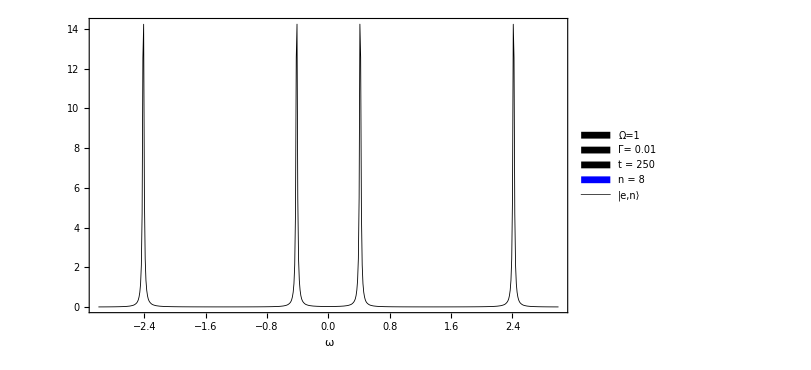

```mathematica
ListLinePlot[ParallelTable[{ω,MollowDetuning[1,0.01,ω,500,1]},{ω,-3,3,0.01}],
PlotRange->All,Frame->True,ImageSize->600,
Axes->None,FrameTicksStyle->20,
PlotStyle->Directive[Black,Thickness[0.001]],
FrameLabel->{{None,None},{Style["ω",30],
 Style["Spectrum-JCM" ,30]}},
PlotLegends->{Placed[SwatchLegend[{Black,Black,Black,Blue},
{Style["Ω=1",20],Style["Γ= 0.01",20],
Style["t = 250",20],Style["n = 8",20]}],{.9,.8}],
Placed[LineLegend[{Style["|e,n⟩",25,Black]},LegendFunction->(Framed[#,RoundingRadius->2,Background->White]&)],{0.11,0.9}]}]
```

Estado inicial |g,α ⟩, donde |α ⟩ es un estado coherente

```mathematica
Δ = 0.0;
```

```mathematica
SepectroEstadoCoherente[Ω_,Γ_,ω_,t_,α_]:=Exp[-Abs[α]^2]Sum[Abs[α]^(2n+2)MollowDetuning[Ω,Γ,ω,t,n]/(n+1)!,{n,0,30}]
```

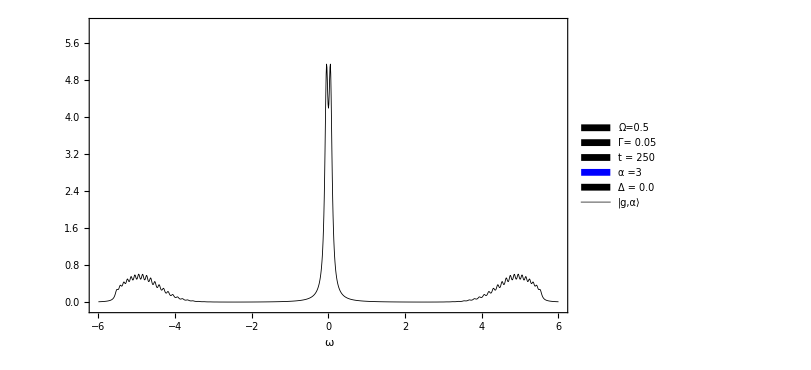

/home/roberto/Documents/SS_OptCuantica/resultados/quantum_model/constant_detuning/linear/try2_zoom/delta=0.0

```mathematica
ListLinePlot[ParallelTable[{ω,SepectroEstadoCoherente[0.5,0.05,ω,250,5]},{ω,-6.0,6.0,0.01}],
PlotRange->{-0.1,6.0},Frame->True,ImageSize->600,
Axes->None,FrameTicksStyle->20,PlotStyle->Directive[Black,Thickness[0.001]],
FrameLabel->{{None,None},{Style["ω",30],Style["Spectrum-JCM" ,30]}},PlotLegends->{Placed[SwatchLegend[{Black,Black,Black,Blue,Black},{Style["Ω=0.5",20],Style["Γ= 0.05",20],Style["t = 250",20],Style["α =3",20],Style["Δ = 0.0",20]}],{.9,.8}],
Placed[LineLegend[{Style["|g,α⟩",25,Black]},LegendFunction->(Framed[#,RoundingRadius->2,Background->White]&)],{0.11,0.9}]}]
```

## Resonancia

```mathematica
Assuming[Ω>0&&n>0&&t>0&&Γ>0&&ω>0,Integrate[Exp[(Γ-I ω)t1]Sin[Ω Sqrt[n+1]t1]Sin[Ω Sqrt[n]t1],{t1,0,t}]]
```

(ⅇ^(-ⅈ t ω) (-ⅇ^(t Γ) √(1+n) Ω (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2) Cos[√(1+n) t Ω] Sin[√n t Ω]+ⅇ^(t Γ) Ω Cos[√n t Ω] (2 √(n (1+n)) (Γ-ⅈ ω) Ω Cos[√(1+n) t Ω]+√n (-Γ^2+2 ⅈ Γ ω+ω^2+Ω^2) Sin[√(1+n) t Ω])+(Γ-ⅈ ω) (-2 ⅇ^(ⅈ t ω) √(n (1+n)) Ω^2+ⅇ^(t Γ) (Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n) Ω^2) Sin[√n t Ω] Sin[√(1+n) t Ω])))/((Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n-2 √(n (1+n))) Ω^2) (Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n+2 √(n (1+n))) Ω^2))

```mathematica
R1[Ω_,n_,Γ_,ω_,t_]:=(ⅇ^(-ⅈ t ω) (-ⅇ^(t Γ) √(1+n) Ω (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2) Cos[√(1+n) t Ω] Sin[√n t Ω]+ⅇ^(t Γ) Ω Cos[√n t Ω] (2 √(n (1+n)) (Γ-ⅈ ω) Ω Cos[√(1+n) t Ω]+√n (-Γ^2+2 ⅈ Γ ω+ω^2+Ω^2) Sin[√(1+n) t Ω])+(Γ-ⅈ ω) (-2 ⅇ^(ⅈ t ω) √(n (1+n)) Ω^2+ⅇ^(t Γ) (Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n) Ω^2) Sin[√n t Ω] Sin[√(1+n) t Ω])))/((Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n-2 √(n (1+n))) Ω^2) (Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n+2 √(n (1+n))) Ω^2))
```

```mathematica
Assuming[Ω>0&&n>0&&t>0&&Γ>0&&ω>0,Integrate[Exp[(Γ-I ω)t1]Sin[Ω Sqrt[n+1]t1]Cos[Ω Sqrt[n]t1],{t1,0,t}]]
```

```mathematica
(ⅇ^(-ⅈ t ω) (ⅇ^(t Γ) Cos[√n t Ω] (-√(1+n) Ω (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2) Cos[√(1+n) t Ω]+(Γ-ⅈ ω) (Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n) Ω^2) Sin[√(1+n) t Ω])+Ω (ⅇ^(ⅈ t ω) √(1+n) (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2)-2 ⅇ^(t Γ) √(n (1+n)) (Γ-ⅈ ω) Ω Cos[√(1+n) t Ω] Sin[√n t Ω]+ⅇ^(t Γ) √n (Γ^2-2 ⅈ Γ ω-ω^2-Ω^2) Sin[√n t Ω] Sin[√(1+n) t Ω])))/((Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n-2 √(n (1+n))) Ω^2) (Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n+2 √(n (1+n))) Ω^2))
```

(ⅇ^(-ⅈ t ω) (ⅇ^(t Γ) Cos[√n t Ω] (-√(1+n) Ω (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2) Cos[√(1+n) t Ω]+(Γ-ⅈ ω) (Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n) Ω^2) Sin[√(1+n) t Ω])+Ω (ⅇ^(ⅈ t ω) √(1+n) (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2)-2 ⅇ^(t Γ) √(n (1+n)) (Γ-ⅈ ω) Ω Cos[√(1+n) t Ω] Sin[√n t Ω]+ⅇ^(t Γ) √n (Γ^2-2 ⅈ Γ ω-ω^2-Ω^2) Sin[√n t Ω] Sin[√(1+n) t Ω])))/((Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n-2 √(n (1+n))) Ω^2) (Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n+2 √(n (1+n))) Ω^2))

```mathematica
R2[Ω_,n_,Γ_,ω_,t_]:=(ⅇ^(-ⅈ t ω) (ⅇ^(t Γ) Cos[√n t Ω] (-√(1+n) Ω (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2) Cos[√(1+n) t Ω]+(Γ-ⅈ ω) (Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n) Ω^2) Sin[√(1+n) t Ω])+Ω (ⅇ^(ⅈ t ω) √(1+n) (Γ^2-2 ⅈ Γ ω-ω^2+Ω^2)-2 ⅇ^(t Γ) √(n (1+n)) (Γ-ⅈ ω) Ω Cos[√(1+n) t Ω] Sin[√n t Ω]+ⅇ^(t Γ) √n (Γ^2-2 ⅈ Γ ω-ω^2-Ω^2) Sin[√n t Ω] Sin[√(1+n) t Ω])))/((Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n-2 √(n (1+n))) Ω^2) (Γ^2-2 ⅈ Γ ω-ω^2+(1+2 n+2 √(n (1+n))) Ω^2))
```

```mathematica
SepectroJCM[Ω_,Γ_,ω_,t_,n_]:=2Γ Exp[-2Γ t](Abs[R1[Ω,n,Γ,ω,t]]^2+Abs[R2[Ω,n,Γ,ω,t]]^2)
```

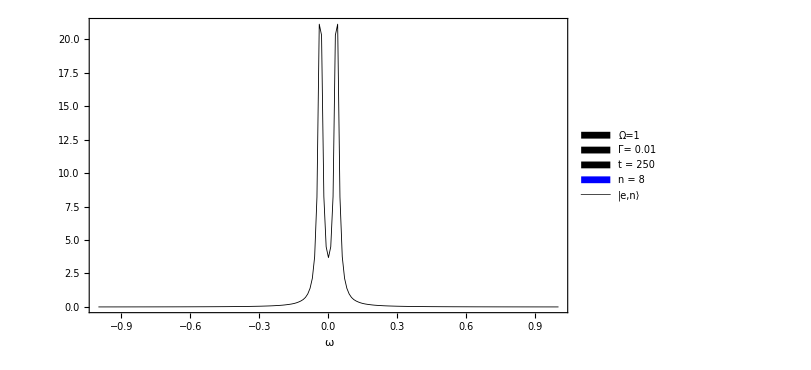

```mathematica
ListLinePlot[ParallelTable[{ω,SepectroJCM[1,0.01,ω,500,200]},{ω,-1,1,0.01}],
PlotRange->All,Frame->True,ImageSize->600,Axes->None,FrameTicksStyle->20,PlotStyle->Directive[Black,Thickness[0.001]],FrameLabel->{{None,None},{Style["ω",30],
 Style["Spectrum-JCM" ,30]}},PlotLegends->{Placed[SwatchLegend[{Black,Black,Black,Blue},
{Style["Ω=1",20],Style["Γ= 0.01",20],Style["t = 250",20],Style["n = 8",20]}],{.9,.8}],Placed[LineLegend[{Style["|e,n⟩",25,Black]},LegendFunction->(Framed[#,RoundingRadius->2,Background->White]&)],{0.11,0.9}]}]
```

## Sistema 1

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Sin[(t Ωn)/2], {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t](Sin[t Ωn]/2+(I Δ)/Ωn(Sin[(t Ωn)/2]^2)), {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
S[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T]((((2 g Sqrt[n+1])/Ωn)^4)I1[Γ, ω,T, T0]+(((2 g Sqrt[n+1])/Ωn)^2)I2[Γ, ω,T,T0])
```

```mathematica
Γ = 0.01;T = 500;T0=-140; Δ= 0.0;g=0.1;n=1;
```

```mathematica
Ωn = Sqrt[4(n+1)g^2 + Δ^2]
```

0.282843

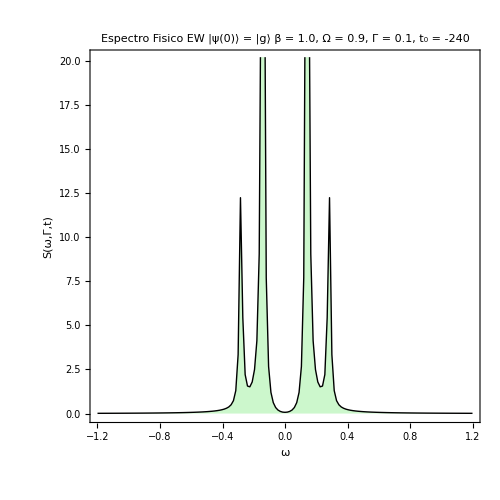

```mathematica
ListLinePlot[ParallelTable[{ω,S[Γ,ω,T,T0]},{ω,-1.2,1.2,0.015}],PlotRange->{-0.1,20.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
 ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],PlotLegends->"t=-10",
 PlotLabel->Style["Espectro Fisico EW   |ψ(0)⟩ = |g⟩ \n β = 1.0, Ω = 0.9, Γ = 0.1, t_0 = -240", 16, FontFamily->"Times New Roman", Black]]
```

## Sistema 2

```mathematica
DSolve[x'[t]==- I Ω-I (β^2)t x[t]+I Ω x[t]^2,x[t],t]
```

{{x[t]→(ⅈ (C[1] (-ⅈ ⅇ^(-1/2 ⅈ t^2 β^2) t β^2 HermiteH[(-β^2-ⅈ Ω^2)/β^2,((-1)^(1/4) t β)/(√2)]+((-1)^(1/4) √2 ⅇ^(-1/2 ⅈ t^2 β^2) (-β^2-ⅈ Ω^2) HermiteH[-1+(-β^2-ⅈ Ω^2)/β^2,((-1)^(1/4) t β)/(√2)])/β)-ⅈ ⅇ^(-1/2 ⅈ t^2 β^2) t β^2 Hypergeometric1F1[-(-β^2-ⅈ Ω^2)/(2 β^2),1/2,1/2 ⅈ t^2 β^2]-ⅈ ⅇ^(-1/2 ⅈ t^2 β^2) t (-β^2-ⅈ Ω^2) Hypergeometric1F1[1-(-β^2-ⅈ Ω^2)/(2 β^2),3/2,1/2 ⅈ t^2 β^2]))/(Ω (ⅇ^(-1/2 ⅈ t^2 β^2) C[1] HermiteH[(-β^2-ⅈ Ω^2)/β^2,((-1)^(1/4) t β)/(√2)]+ⅇ^(-1/2 ⅈ t^2 β^2) Hypergeometric1F1[-(-β^2-ⅈ Ω^2)/(2 β^2),1/2,1/2 ⅈ t^2 β^2]))}}

```mathematica
β = 0.1; Ω = 0.1;n=6;
```

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + I Ω Sqrt[n+1](1 + x[t]^2)== 0 ,y'[t] == I(Ω Sqrt[n+1] x[t] - ((β^2 )t)/2),z'[t]Exp[-2 y[t]]+ I Ω Sqrt[n+1] == 0, x[-150]==y[-150]==z[-150]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10];
```

```mathematica
alphaMasInterp = Interpolation[Table[{t, alphaMas[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

```mathematica
alphaMenosInterp = Interpolation[Table[{t, alphaMenos[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

```mathematica
alphaZInterp = Interpolation[Table[{t,alphaZ[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

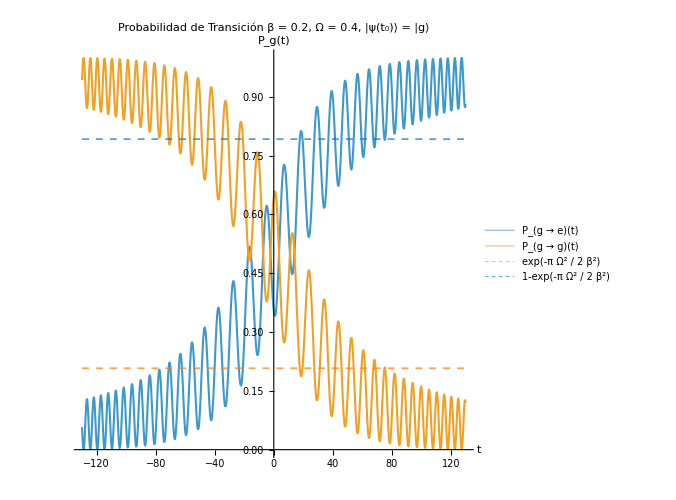

```mathematica
Plot[{(Abs[alphaMasInterp[t]]^2 )Exp[-2Re[alphaZInterp[t]]], Abs[Exp[- alphaZInterp[t]] ]^2,Exp[-π(Ω^2/(2(β^2)))], 1- Exp[-π(Ω^2/(2β^2))]}, {t, -130, 130}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)","exp(-π Ω^2 / 2 β^2)","1-exp(-π Ω^2 / 2 β^2)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,
PlotLabel->Style["Probabilidad de Transición  β = 0.2, Ω = 0.4, |ψ(t_0)⟩ = |g⟩ ", 18, FontFamily->"Times New Roman", Black]]
```

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZInterp[t]]alphaMenosInterp[t]^2, {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZInterp[t]]alphaMenosInterp[t],{t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
Γ = 0.01;T = 10;T0=-200;
```

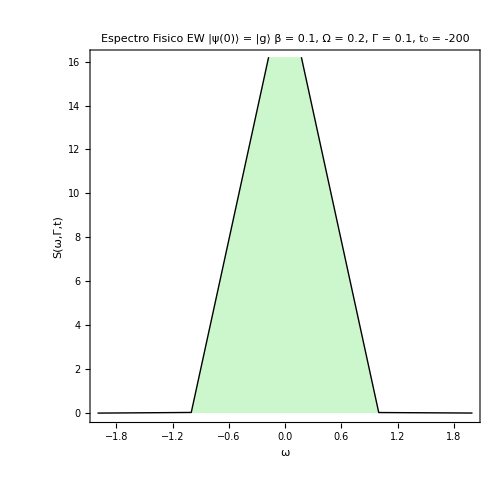

```mathematica
ListLinePlot[ParallelTable[{ω,S[Γ,ω,T,T0]},{ω,-2,2}],PlotRange->{-0.1,16.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->{{14,2},{14,20}},PlotRangePadding->0,AspectRatio->1,FrameLabel->{Style["ω",16,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",16,FontFamily->"Times New Roman",Gray]},
 ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]], PlotLabel->Style["Espectro Fisico EW   |ψ(0)⟩ = |g⟩ \n β = 0.1, Ω = 0.2, Γ = 0.1, t_0 = -200", 16, FontFamily->"Times New Roman", Black]]
```